```mathematica
g=9.81;
r=1;
patm=1.2;
phe=0.178;
mb=2;
mp=1;
cd=1;
S=Pi*r^2;
V=4/3*Pi*r^3;
mHe=V*phe;
```

```mathematica
a=mHe+mb+mp;
b=0.5*S*cd*patm;
c=V*g*(-phe+patm)-g*(mb+mp);
```

{569.527+12.5664 y[x]^2-8.96484 y'[x]==0,True}

```mathematica
sol=DSolve[{-a*y'[x]+b*y[x]^2+c==0,y[0]==0},y,{x,0,5}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y→Function[{x},2.58196 Tan[1.29936 x]]}}

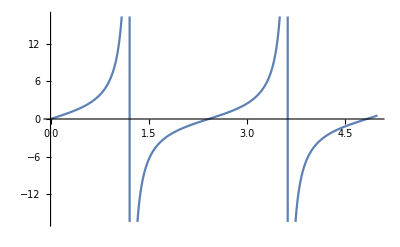

```mathematica
Plot[y[x]/.sol,{x,0,5}]
```